### Start choosing the example:

```mathematica
t=14;
beta = 1;
A =0;
Get["/Users/salehfh/downloads/MFGraphs-master/MFGraphs/Examples/ExamplesParameters.m"]
g[x]
```

x

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesData.m"];
```

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{3,U1}},Switching Costs→{{1,2,3,S1},{3,2,1,S2}}|>

```mathematica
(rule=CriticalCongestionSolver2[d2e=D2E[Data/.{I1->1,U1->0,S1->1, S2->0}]])//AbsoluteTiming
```

Variables are all set

Assembled most elements of the system

CleanEqualities for the switching conditions on each vertex

CleanEqualities for the complementary conditions (given the rules)

CleanEqualities for the values at the auxiliary edges

CleanEqualities for the balance conditions in terms of (mostly) transition currents

CleanEqualities for the (non) critical case equations

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

{0.081326,<|u1→1,u2→1,u3→0,u4→0,u5→0,u6→1,u7→0,u8→0,u9→1,u10→1,j1→0,j2→0,j3→0,j4→0,j5→1,j6→0,j7→0,j8→1,j9→0,j10→1|>}

## Non-critical congestion

```mathematica
Cost[current_,edge_]
```

IntM[current_,edge_]

```mathematica
Cost[a_,b_]:= -a
```

```mathematica
Cost[a_,b_]:= 0
```

```mathematica
d2e=D2E[Data/.{I1->1,U1->0,S1->1, S2->0}];
```

Variables are all set

Assembled most elements of the system

CleanEqualities for the switching conditions on each vertex

CleanEqualities for the complementary conditions (given the rules)

CleanEqualities for the values at the auxiliary edges

CleanEqualities for the balance conditions in terms of (mostly) transition currents

CleanEqualities for the (non) critical case equations

```mathematica
alpha =0;
FFR=FixedPoint[FixedReduce2[d2e],<||>,10]
```

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

<|u1→17599210499/15000000000,u2→32599210499/30000000000,u3→2599210499/30000000000,u4→0,u5→0,u6→17599210499/15000000000,u7→0,u8→0,u9→17599210499/15000000000,u10→17599210499/15000000000,j1→0,j2→2599210499/30000000000,j3→0,j4→2599210499/30000000000,j5→27400789501/30000000000,j6→0,j7→0,j8→1,j9→0,j10→1|>

```mathematica
alpha =0.5;
FFR=FixedPoint[FixedReduce2[d2e],<||>,10]
```

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

<|u1→329739671/300000000,u2→629739671/600000000,u3→29739671/600000000,u4→0,u5→0,u6→329739671/300000000,u7→0,u8→0,u9→329739671/300000000,u10→329739671/300000000,j1→0,j2→29739671/600000000,j3→0,j4→29739671/600000000,j5→570260329/600000000,j6→0,j7→0,j8→1,j9→0,j10→1|>

```mathematica
alpha =1;
FFR=FixedPoint[FixedReduce2[d2e],<||>,10]
```

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

<|u1→1,u2→1,u3→0,u4→0,u5→0,u6→1,u7→0,u8→0,u9→1,u10→1,j1→0,j2→0,j3→0,j4→0,j5→1,j6→0,j7→0,j8→1,j9→0,j10→1|>

```mathematica
alpha =1.5;
FFR=FixedPoint[FixedReduce2[d2e],<||>,10]
```

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

<|u1→396850263/500000000,u2→396850263/500000000,u3→0,u4→0,u5→0,u6→396850263/500000000,u7→0,u8→0,u9→396850263/500000000,u10→396850263/500000000,j1→0,j2→0,j3→0,j4→0,j5→1,j6→0,j7→0,j8→1,j9→0,j10→1|>

```mathematica
alpha =2;
FFR=FixedPoint[FixedReduce2[d2e],<||>,10]
```

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

<|u1→1/2,u2→1/2,u3→0,u4→0,u5→0,u6→1/2,u7→0,u8→0,u9→1/2,u10→1/2,j1→0,j2→0,j3→0,j4→0,j5→1,j6→0,j7→0,j8→1,j9→0,j10→1|>

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{3,U1}},Switching Costs→{{1,2,3,S1},{3,2,1,S2}}|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1->1,U1->0,S1->1, S2->0}];//Timing
MFGEquations["jvars"]/.MFGEquations["criticalreduced1"][[2]]//KeySort
MFGEquations["uvars"]/.MFGEquations["criticalreduced1"][[2]]//KeySort
```

DataToEquations: Triangle inequalities for switching costs: {True,True}
DataToEquations: Reduced: True

The switching costs are compatible.

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 0.139068 seconds to reduce with NewReduce!

DataToEquations: After NewReduce, the system is:
j946==0&&j951==1&&jt954==0&&u968==1&&u969==0&&u970==0&&u972==1
and the rules are:
<|j948→1,u976→0,j944→1+j946-j951+jt954,j945→1+j946-j951+jt954,j947→1,j949→jt954,j950→jt954,j952→0,j953→0,jt955→0,jt956→j946,jt957→0,jt958→1-j951+jt954,jt959→j951-jt954,jt960→1+j946-j951+jt954,jt961→jt954,jt962→j946,jt963→1-j951+jt954,jt964→jt954,jt965→j951-jt954,jt966→0,jt967→0,u971→0,u973→-1-j946+j951+u968,u974→-1-j946+j951+u969,u975→-j946+j951+u970,u977→u972|>

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.166185,Null}

<|{1,1->2}→0,{1,3->1}→0,{1,en942->1}→1,{2,1->2}→0,{2,2->3}→0,{3,2->3}→0,{3,3->1}→1,{3,3->ex943}→0,{en942,en942->1}→0,{ex943,3->ex943}→1|>

<|{1,1->2}→1,{1,3->1}→1,{1,en942->1}→1,{2,1->2}→1,{2,2->3}→0,{3,2->3}→0,{3,3->1}→0,{3,3->ex943}→0,{en942,en942->1}→1,{ex943,3->ex943}→0|>

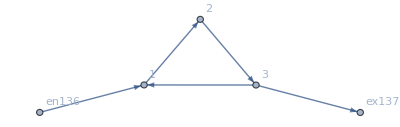

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j524→2/9,j525→2/9,j526→0,j527→1,j528→1,j529→0,j530→0,j531→7/9,j532→0,j533→0,jt534→0,jt535→0,jt536→0,jt537→0,jt538→2/9,jt539→7/9,jt540→2/9,jt541→0,jt542→0,jt543→2/9,jt544→0,jt545→7/9,jt546→0,jt547→0,u548→7/9,u549→2/9,u550→0,u551→0,u552→7/9,u553→5/9,u554→0,u555→7/9,u556→0,u557→7/9|>

```mathematica
<|j452->1/3,j453->1/3,j454->0,j455->1,j456->1,j457->0,j458->0,j459->2/3,j460->0,j461->0,jt462->0,jt463->0,jt464->0,jt465->0,jt466->1/3,jt467->2/3,jt468->1/3,jt469->0,jt470->0,jt471->1/3,jt472->0,jt473->2/3,jt474->0,jt475->0,u476->17/3,u477->16/3,u478->5,u479->5,u480->17/3,u481->16/3,u482->5,u483->17/3,u484->5,u485->17/3|>
```

<|j452→1/3,j453→1/3,j454→0,j455→1,j456→1,j457→0,j458→0,j459→2/3,j460→0,j461→0,jt462→0,jt463→0,jt464→0,jt465→0,jt466→1/3,jt467→2/3,jt468→1/3,jt469→0,jt470→0,jt471→1/3,jt472→0,jt473→2/3,jt474→0,jt475→0,u476→17/3,u477→16/3,u478→5,u479→5,u480→17/3,u481→16/3,u482→5,u483→17/3,u484→5,u485→17/3|>

#### Non-linear case

```mathematica
alpha = 0;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j138→0,j139→0,j140→0,j141→10,j142→10,j143→0,j144→0,j145→10,j146→0,j147→0,jt148→0,jt149→0,jt150→0,jt151→0,jt152→0,jt153→10,jt154→0,jt155→0,jt156→0,jt157→0,jt158→0,jt159→10,jt160→0,jt161→0,u162→7.71442,u163→5.,u164→5.,u165→5,u166→7.71442,u167→7.71442,u168→5.,u169→7.71442,u170→5,u171→7.71442|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j138→0,j139→0,j140→0,j141→10,j142→10,j143→0,j144→0,j145→10,j146→0,j147→0,jt148→0,jt149→0,jt150→0,jt151→0,jt152→0,jt153→10,jt154→0,jt155→0,jt156→0,jt157→0,jt158→0,jt159→10,jt160→0,jt161→0,u162→7.96984,u163→5.,u164→5.,u165→5,u166→7.96984,u167→7.96984,u168→5.,u169→7.96984,u170→5,u171→7.96984|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 6.9681×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 6.9681×10^-17

<|j138→0,j139→0,j140→0,j141→10,j142→10,j143→0,j144→0,j145→10,j146→0,j147→0,jt148→0,jt149→0,jt150→0,jt151→0,jt152→0,jt153→10,jt154→0,jt155→0,jt156→0,jt157→0,jt158→0,jt159→10,jt160→0,jt161→0,u162→8.62682,u163→5.,u164→5.,u165→5,u166→8.62682,u167→8.62682,u168→5.,u169→8.62682,u170→5,u171→8.62682|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j138→0,j139→0,j140→0,j141→10,j142→10,j143→0,j144→0,j145→10,j146→0,j147→0,jt148→0,jt149→0,jt150→0,jt151→0,jt152→0,jt153→10,jt154→0,jt155→0,jt156→0,jt157→0,jt158→0,jt159→10,jt160→0,jt161→0,u162→13.3004,u163→5.,u164→5.,u165→5,u166→13.3004,u167→13.3004,u168→5.,u169→13.3004,u170→5,u171→13.3004|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1.06581×10^-14,ComplexInfinity]

<|j138→0,j139→0,j140→0,j141→10,j142→10,j143→0,j144→0,j145→10,j146→0,j147→0,jt148→0,jt149→0,jt150→0,jt151→0,jt152→0,jt153→10,jt154→0,jt155→0,jt156→0,jt157→0,jt158→0,jt159→10,jt160→0,jt161→0,u162→15,u163→5,u164→5,u165→5,u166→15,u167→15,u168→5,u169→15,u170→5,u171→15|>

```mathematica
alpha = 1.7;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j210→0,j211→0,j212→0,j213→10,j214→10,j215→0,j216→0,j217→10,j218→0,j219→0,jt220→0,jt221→0,jt222→0,jt223→0,jt224→0,jt225→10,jt226→0,jt227→0,jt228→0,jt229→0,jt230→0,jt231→10,jt232→0,jt233→0,u234→87.1921,u235→5.,u236→5.,u237→5,u238→87.1921,u239→87.1921,u240→5.,u241→87.1921,u242→5,u243→87.1921|>

```mathematica
alpha = 1.77;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.890369

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.963772

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.00707

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.00001

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

«3 more identical outputs»

<|j210→0,j211→0,j212→0,j213→10,j214→10,j215→1.41033×10^214,j216→1.41033×10^214,j217→1.41033×10^214,j218→0,j219→0,jt220→1.41033×10^214,jt221→0,jt222→0,jt223→0,jt224→0,jt225→10,jt226→0,jt227→1.41033×10^214,jt228→0,jt229→0,jt230→1.41033×10^214,jt231→10,jt232→0,jt233→0,u234→0,u235→0.,u236→5.,u237→5,u238→0.,u239→0.,u240→5.,u241→0.,u242→5,u243→0.|>

```mathematica
alpha = 1.8;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],4,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j138→0,j139→0,j140→0,j141→10,j142→10,j143→0,j144→0,j145→10,j146→0,j147→0,jt148→0,jt149→0,jt150→0,jt151→0,jt152→0,jt153→10,jt154→0,jt155→0,jt156→0,jt157→0,jt158→0,jt159→10,jt160→0,jt161→0,u162→140.721,u163→5.,u164→5.,u165→5,u166→140.721,u167→140.721,u168→5.,u169→140.721,u170→5,u171→140.721|>

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.00359

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

«3 more identical outputs»

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[√(Abs[-1.42247815737932×10^354-1. j211+1. j216-IntM[-10+j211-j216]]^2+Abs[-1.42247815737932×10^354-1. j211+1. j216-IntM[j211-j216]]^2+Abs[-1.42247815737932×10^354-1. j211+1. j216+0. u234-IntM[j211-j216]]^2),(√(Abs[-1.42247815737932×10^354-1. j211+1. j216-IntM[-10+j211-j216]]^2+Abs[-1.42247815737932×10^354-1. j211+1. j216-IntM[j211-j216]]^2+Abs[-1.42247815737932×10^354-1. j211+1. j216+0. u234-IntM[j211-j216]]^2))/(√(2 Abs[-1.42247815737932×10^354+0. j211+0. j216]^2+Abs[-1.42247815737932×10^354+0. j211+0. j216+0. u234]^2)),(√(Abs[-1.42247815737932×10^354-1. j211+1. j216-IntM[-10+j211-j216]]^2+Abs[-1.42247815737932×10^354-1. j211+1. j216-IntM[j211-j216]]^2+Abs[-1.42247815737932×10^354-1. j211+1. j216+0. u234-IntM[j211-j216]]^2))/(√(Abs[-10+j211-j216+IntM[-10+j211-j216]]^2+2 Abs[j211-j216+IntM[j211-j216]]^2))]

ReplaceAll::reps: {u236==5&&u238==u241&&u240==5&&j211-j216-u234+u239==j211-j216+IntM[j211-j216]&&j211-j216-u235+u240==j211-j216+IntM[j211-j216]&&-10+j211-j216-u236+u241==-10+j211-j216+IntM[-10+j211-j216]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

AssociateTo::invlb: The argument u236==5&&u238==u241&&u240==5&&j211-j216-u234+u239==j211-j216+IntM[j211-j216]&&j211-j216-u235+u240==j211-j216+IntM[j211-j216]&&-10+j211-j216-u236+u241==-10+j211-j216+IntM[-10+j211-j216] is not a list, Rule, or Association.

ReplaceAll::reps: {u236==5&&u238==u241&&u240==5&&j211-j216-u234+u239==j211-j216+IntM[j211-j216]&&j211-j216-u235+u240==j211-j216+IntM[j211-j216]&&-10+j211-j216-u236+u241==-10+j211-j216+IntM[-10+j211-j216]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$Aborted

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],9,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.00012

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1.,ComplexInfinity]

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.00012

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1.,ComplexInfinity]

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.00012

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1.,ComplexInfinity]

<|j210→0,j211→0,j212→0,j213→10,j214→10,j215→0,j216→0,j217→10,j218→0,j219→0,jt220→0,jt221→0,jt222→0,jt223→0,jt224→0,jt225→10,jt226→0,jt227→0,jt228→0,jt229→0,jt230→0,jt231→10,jt232→0,jt233→0,u234→15,u235→5,u236→5,u237→5,u238→15,u239→15,u240→5,u241→15,u242→5,u243→15|>